Background

```mathematica
coord ={t,r,θ1,θ2,θ3};
metric=({{-Λ/(6 r^2)(r^2-re^2)(rc^2-r^2), 0, 0, 0, 0}, {0, 1/(Λ/(6 r^2)(r^2-re^2)(rc^2-r^2)), 0, 0, 0}, {0, 0, r^2, 0, 0}, {0, 0, 0, r^2 Sin[θ1]^2, 0}, {0, 0, 0, 0, r^2 Sin[θ1]^2 Sin[θ2]^2}});
```

```mathematica
$Assumptions= And[t∈Reals,ω∈Reals,ϵ>0];
metricsign=-1;
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<diffgeo.m
```

```mathematica
EEstep1 = RicciTensor-1/2 RicciScalar*metric  + Λ* metric;
```

```mathematica
EEstep2 = EEstep1  /.re->((3-Sqrt[9-12MΛ])/Λ)^(1/2)/.rc->((3+Sqrt[9-12MΛ])/Λ)^(1/2)//FullSimplify
```

{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}

```mathematica
Riemann;
```

```mathematica
contract[lower[Riemann,{4}]**lower[Riemann,{4}],{1,5},{2,6},{3,7},{4,8}]/.re->((3-Sqrt[9-12MΛ])/Λ)^(1/2)/.rc->((3+Sqrt[9-12MΛ])/Λ)^(1/2)//FullSimplify
```

(288 MΛ^2)/(r^8 Λ^2)+(10 Λ^2)/9

Perturbation

```mathematica
Φ=Exp[-ⅈ*ω*t]*Ψ[r]
```

ⅇ^(-ⅈ t ω) Ψ[r]

```mathematica
SEstep1=scalarLaplacian[Φ] //Simplify;
SEstep2=Collect[(SEstep1/Exp[-ⅈ*ω*t]-(l(l+2))/r^2 Ψ[r]),{Ψ''[r],Ψ'[r],Ψ[r]},Simplify]
```

(-(l (2+l))/r^2-(6 r^2 ω^2)/((r^2-rc^2) (r^2-re^2) Λ)) Ψ[r]-((5 r^4+rc^2 re^2-3 r^2 (rc^2+re^2)) Λ Ψ'[r])/(6 r^3)-((r^2-rc^2) (r^2-re^2) Λ Ψ''[r])/(6 r^2)

```mathematica
c[r_]=(-(l (2+l))/r^2-(6 r^2 ω^2)/((r^2-rc^2) (r^2-re^2) Λ))//FullSimplify;
b[r_]=-((5 r^4+rc^2 re^2-3 r^2 (rc^2+re^2)) Λ)/(6 r^3)//FullSimplify;
a[r_]=-((r^2-rc^2) (r^2-re^2) Λ)/(6 r^2)//FullSimplify;
```

```mathematica
V0[r_]=-1/(4 a[r]^2)(2b[r]*a'[r]-b[r]^2-2a[r]*(b'[r]-2c[r]));
DetermiV0[r_]=Collect[(4 r^2 (r^2-rc^2)^2 (r^2-re^2)^2 Λ^2)V0[r]//FullSimplify,r] 
V[r_]=-1/(4 a[r]^2)(2b[r]*a'[r]-b[r]^2-2a[r]*(b'[r]-2c[r]))/.re->Sqrt[1]/.rc->Sqrt[5]/.Λ->1//FullSimplify
```

15 r^8 Λ^2-rc^4 re^4 Λ^2+r^2 (-48 l rc^2 re^2 Λ-24 l^2 rc^2 re^2 Λ-6 rc^2 re^2 (rc^2+re^2) Λ^2)+r^4 (48 l rc^2 Λ+24 l^2 rc^2 Λ+48 l re^2 Λ+24 l^2 re^2 Λ+3 (rc^4+12 rc^2 re^2+re^4) Λ^2)+r^6 (-48 l Λ-24 l^2 Λ-22 (rc^2+re^2) Λ^2-144 ω^2)

(-25-60 (3+2 l (2+l)) r^2+6 (43+24 l (2+l)) r^4+15 r^8-12 r^6 (11+2 l (2+l)+12 ω^2))/(4 r^2 (5-6 r^2+r^4)^2)

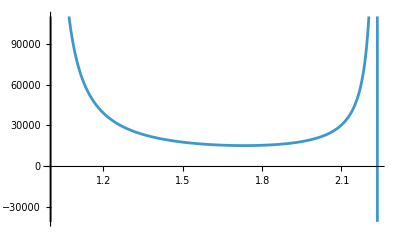

```mathematica
Plot[V[r]/.ω->0.1/.l->100,{r,Sqrt[1],Sqrt[5]}]
```

```mathematica
Vevent0[ϵ_]=Collect[Normal[Series[V0[r],{r,re,0}]]/.r->re+ϵ/.re->((3-Sqrt[9-12MΛ])/Λ)^(1/2)/.rc->((3+Sqrt[9-12MΛ])/Λ)^(1/2)//FullSimplify,ϵ];
Vcosmo0[ϵ_]=Collect[Normal[Series[V0[r],{r,rc,0}]]/.r->rc-ϵ/.re->((3-Sqrt[9-12MΛ])/Λ)^(1/2)/.rc->((3+Sqrt[9-12MΛ])/Λ)^(1/2)//FullSimplify,ϵ];
Vevent[ϵ_]=Normal[Series[V[r],{r,1,0}]]
Vcosmo[ϵ_]=Normal[Series[V[r],{r,Sqrt[5],0}]]
```

(-4-9 ω^2)/(16 (-1+r)^2)+(2+6 l+3 l^2-9 ω^2)/(4 (-1+r))-7/16 (4+9 ω^2)

(-4-45 ω^2)/(16 (-√5+r)^2)+1/20 (-4+18 l+9 l^2-45 ω^2)+(16-12 l-6 l^2+45 ω^2)/(8 √5 (-√5+r))

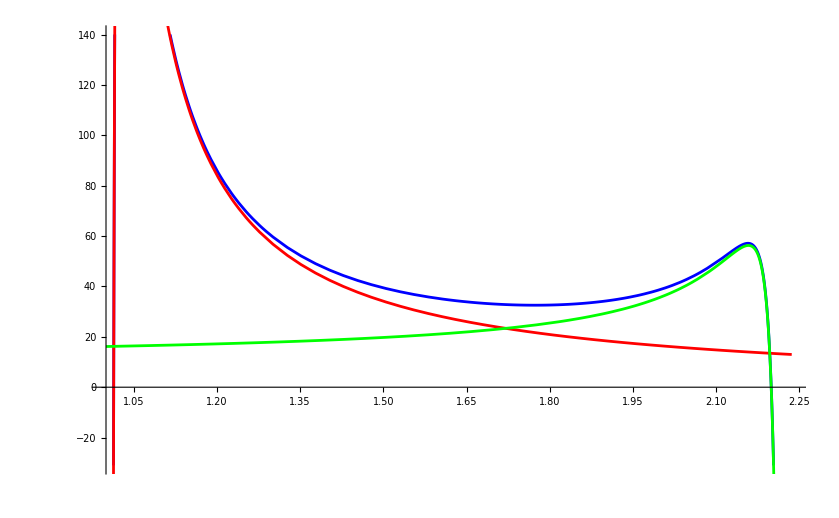

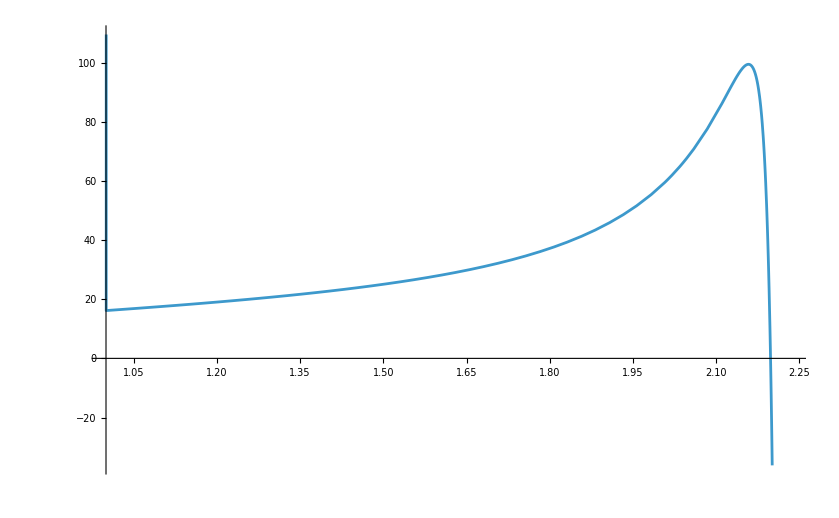

```mathematica
Show[Plot[{V[r]}/.ω->0.1/.l->4,{r,1,Sqrt[5]},PlotStyle->{Blue}],Plot[{Vevent[r]}/.ω->0.1/.l->4,{r,1,Sqrt[5]},PlotStyle->Red],Plot[{Vcosmo[r]}/.ω->0.1/.l->4,{r,1,2.9},PlotStyle->{Green}]]
Plot[V[r]-Vevent[r]+Vcosmo[r]/.ω->0.1/.l->4,{r,1,Sqrt[5]}]
```

```mathematica
Hey[ϵ_]=Integrate[Sqrt[-a+b/ϵ-c/ϵ^2],ϵ]//FullSimplify
```

1/(2 √a √(c+ϵ (-b+a ϵ)))√(-c+ϵ (b-a ϵ)) (2 √a √(c-b ϵ+a ϵ^2)+4 √a √c ArcTanh[(√a ϵ-√(c-b ϵ+a ϵ^2))/(√c)]+b Log[b-2 a ϵ+2 √a √(c-b ϵ+a ϵ^2)])

```mathematica
Hey[ϵ0]-Hey[(-b+Sqrt[b^2-4a c])/(2a)]//Simplify
```

1/(2 √a)(-1/(√((b (b-√(b^2-4 a c)))/a))√((b (-b+√(b^2-4 a c)))/a) (2 √a √((b (b-√(b^2-4 a c)))/a)+4 √a √c ArcTanh[(-b+√(b^2-4 a c)-2 √a √((b (b-√(b^2-4 a c)))/a))/(2 √a √c)]+b Log[2 b-√(b^2-4 a c)+2 √a √((b (b-√(b^2-4 a c)))/a)])+1/(√(c+ϵ0 (-b+a ϵ0)))√(-c+ϵ0 (b-a ϵ0)) (2 √a √(c-b ϵ0+a ϵ0^2)+4 √a √c ArcTanh[(√a ϵ0-√(c-b ϵ0+a ϵ0^2))/(√c)]+b Log[b-2 a ϵ0+2 √a √(c-b ϵ0+a ϵ0^2)]))

```mathematica
Integrate[Sqrt[V[r]],r]//FullSimplify
```

1/2 ∫√((-25-60 (3+2 l (2+l)) r^2+6 (43+24 l (2+l)) r^4+15 r^8-12 r^6 (11+2 l (2+l)+12 ω^2))/(r^2 (5-6 r^2+r^4)^2))ⅆr